# Arc Length and Surface Area

Goals of this Lab:
This lab is intended to help students:
1.  Set up integrals using the arc length formula to solve problems of interest.
2.  Use numerical integration to evaluate integrals.
3.  Introduce the surface area of revolution.

What you are required to do:
1. Read through this notebook, evaluating cells as needed.
2. Complete the associated quiz in Canvas.

Due Date:
see Canvas

## The Arc Length Formula

To calculate the arc length of a function f, we can divide the whole arc into small pieces, then, the arc length is the sum of the lengths of these small pieces. For each piece, the arc length of this small pieces can be approximated by the hypotenuse of a triangle. Therefore, the whole arc length can be approximated by the sum of all hypotenuses. As shown in the textbook, let the length of each small arc as ⅆs =√(1+[f'(x)]^2)ⅆx=√(1+(ⅆy/ⅆx)^2)ⅆx, if the derivative of f is continuous on [a, b], then the length of the curve y = f (x) for a ≤ x ≤ b is given by
L =∫_a^b ⅆs = ∫_a^b √(1+[f'(x)]^2)ⅆx=∫_a^b √(1+(ⅆy/ⅆx)^2)ⅆx.

If we rewrite ⅆs =√(1+(ⅆy/ⅆx)^2)ⅆx in the symmetric form (ⅆs)^2=(ⅆx)^2 +(ⅆy)^2, then ⅆs =√(1+(ⅆx/ⅆy)^2)ⅆy. The length of the curve x = g (y) for c ≤ y ≤ d is given by
L =∫_a^b ⅆs = ∫_a^b √(1+[g'(y)]^2)ⅆy=∫_a^b √(1+(ⅆx/ⅆy)^2)ⅆy .


The square root sign in this formula often produces an integral that is very difficult (perhaps impossible) to evaluate exactly.  For that reason, you should use Mathematica’s NIntegrate[ ] command rather than Integrate[ ] when evaluating arc length integrals.

Suppose I want to find the length of the curve y = f (x) = ⅇ^x between x = 0 and x = 1.  According to the formula, I will define the function f (x) and then set up an NIntegrate[ ] command:

2.0035

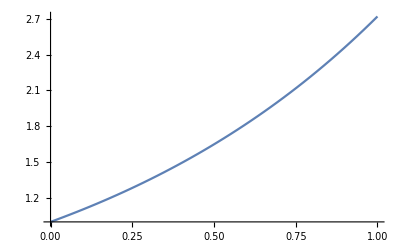

```mathematica
f[x_]=E^x;
NIntegrate[√(1+(f'[x])^2),{x,0,1}]
Plot[f[x],{x,0,1}]
```

For function x = g(y) = ln y between y = 1 and y = ⅇ, then, we can set up the function, calculate the integrate and get the plot.

```mathematica
g[y_]=Log[Cos[2y]];
NIntegrate[√(1+(g'[y])^2),{y,0,π/4}]
```

37.5776

From the two results shown above, the arc length are the same but integrated by different variables.

What could I do to see if my result is feasible?  Note that the points f (0) = 1  and f (1)=ⅇ are on the curve. According to the graph, the straight line distance between these points should be less than the distance along the curve:

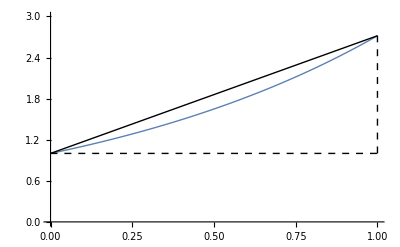

```mathematica
Plot[{f[x]},{x,0,1},PlotStyle->{Thick},PlotRange->{0,3},Epilog->{Thick,Line[{{0,1},{1,E}}],{Dashed,Line[{{0,1},{1,1}}]},{Dashed,Line[{{1,1},{1,E}}]}}]
```

The straight line distance is given by the distance formula: d = √((x_2-x_1)^2+(y_2-y_1)^2)=√((1-0)^2+(ⅇ-1)^2)≈ 1.98809.

## The Arc Length Function

Now suppose we want to have a function that measures the arc length of a curve from a particular starting point to any other point on the curve.  If a smooth curve is described by the equation y = f (x) on [a, b], let s (x) be the distance along the curve from a point (a, f (a)) to a point (x, f (x)) .  The x coordinate of this “destination point” is the argument of our arc length function,
s (x) = ∫_a^x √(1+[f'(u)]^2)ⅆu . 
In this expression, we have replaced the variable of integration by u so that x does not have two meanings.

Let’s give this function a test drive.  Keeping f defined as we have above, let’s “undo” the calculation we just did.  We’re trying to find the value of x that makes this statement true: 
52.0527 = ∫_1^x √(1+[f'(u)]^2)ⅆu.
The FindRoot[ ] command will give us the answer we seek:

```mathematica
f=Sin[(π#)/7]&;
FindRoot[NIntegrate[√(1+(f'[u])^2),{u,1,x}]==50,{x,45}]
```

NIntegrate::nlim: u = x is not a valid limit of integration.

{x→48.7343}

The error message cannot be avoided in this context, so we ignore it.  The 3.5 that appears inside the { } gives Mathematica a starting point for its root search.

## Surface Area

Recall that the surface area of a circular cylinder with radius r and height h is taken to be A=2πrh.

Consider to divide the whole surface area of revolution into several slices. For each slice, we can treat it as a thin cylinder. And when we pile all these thin cylinders together, we can approximate the object of revolution, and the surface area of this object, can be approximated by the sum of all surface area of cylinders. The plot shown below is about the main idea.

As we mentioned above, the tiny piece of arc length ⅆs is defined as ⅆs=√(1+[f'(x)]^2)=√(1+(ⅆy/ⅆx)^2)ⅆx  or  ⅆs=√(1+[g'(y)]^2)ⅆy=√(1+(ⅆx/ⅆy)^2)ⅆy.
Consider to divide along x-axis. For each slice, the height of this cylinder is the tiny arc length ⅆs=√(1+[f'(x)]^2)ⅆx=√(1+(ⅆy/ⅆx)^2)ⅆx,  and the radius of this cylinder is f (x). Then, the surface area of each slice, can be obtained by ⅆS=2π f(x)√(1+[f'(x)]^2)ⅆx=2π f(x)√(1+(ⅆy/ⅆx)^2)ⅆx .

```mathematica
Manipulate[Show[Plot3D[2Sqrt[x],{x,0,4},{y,0,0.1}],RevolutionPlot3D[2Sqrt[t],{t,tt,tt+0.1},{d,0,2Pi},RevolutionAxis->{1, 0, 0},PlotStyle->{Blue}],RevolutionPlot3D[2Sqrt[t],{t,0,4},{d,0,2Pi},RevolutionAxis->{1, 0, 0}],PlotRange->{{-1,5},{-5,5},{-5,5}},LabelStyle->{10,Bold},AxesStyle->Thick,Boxed->False,ViewVertical->{0,0,1},ViewPoint->{0, -1, 0},Axes->{True,False,True},AxesOrigin->{0,0,0}],{tt,0,3.9}]
```

Therefore, in the case where f is positive and has a continuous derivative, we define the surface area of the surface obtained by rotating the curve  y=f(x), a≤ x≤ b, about the x-axis as S=∫_a^b 2πy √(1+[f'(x)]^2)ⅆx=∫_a^b 2πy √(1+(ⅆy/ⅆx)^2)ⅆx.

```mathematica
Manipulate[Show[Plot3D[2Sqrt[x],{x,0,4},{y,0,0.1}],RevolutionPlot3D[2Sqrt[t],{t,2-tt,2+tt},{d,0,dd},RevolutionAxis->{1, 0, 0}],PlotRange->{{-1,5},{-5,5},{-5,5}},LabelStyle->{10,Bold},AxesStyle->Thick,Boxed->False,ViewVertical->{0,0,1},ViewPoint->{0, -1, 0},Axes->{True,False,True},AxesOrigin->{0,0,0}],{dd,0.1,2Pi},{tt,0.05,2}]
```

Consider to divide along y-axis. For each slice, the height of this cylinder is the tiny arc length ⅆs=√(1+[g'(y)]^2)ⅆy=√(1+(ⅆx/ⅆy)^2)ⅆy, and the radius of this cylinder is g (x). Then, the surface area of each slice, can be obtained by ⅆS=2πx √(1+[g'(y)]^2)ⅆy=2πx √(1+(ⅆx/ⅆy)^2)ⅆy.

```mathematica
Manipulate[Show[Plot3D[2Sqrt[x],{x,0,4},{y,0,0.1}],RevolutionPlot3D[2Sqrt[t],{t,tt,tt+0.1},{d,0,2Pi},RevolutionAxis->{0, 0, 1},PlotStyle->{Blue}],RevolutionPlot3D[2Sqrt[t],{t,0,4},{d,0,2Pi},RevolutionAxis->{0, 0, 1}],PlotRange->{{-10,10},{-10,10},{-10,10}},LabelStyle->{10,Bold},ImageSize-> Large,AxesStyle->Thick,Boxed->False,ViewVertical->{0,0,1},ViewPoint->{0, -1, 0.5},Axes->{True,False,True},AxesOrigin->{0,0,0}],{tt,0,3.9}]
```

Therefore, the surface area can be obtained by rotating the curve  x=g(y), c≤ y≤ c, about the y-axis as S=∫_c^d 2πx √(1+[g'(y)]^2)ⅆy=∫_c^d 2πx √(1+(ⅆx/ⅆy)^2)ⅆy.

```mathematica
Manipulate[Show[Plot3D[2Sqrt[x],{x,0,4},{y,0,0.1}],RevolutionPlot3D[2Sqrt[t],{t,2-tt,2+tt},{d,0,dd},RevolutionAxis->{0, 0, 1}],PlotRange->{{-10,10},{-10,10},{-10,10}},LabelStyle->{10,Bold},ImageSize-> Large,AxesStyle->Thick,Boxed->False,ViewVertical->{0,0,1},ViewPoint->{0, -1, 0.5},Axes->{True,False,True},AxesOrigin->{0,0,0}],{dd,0.1,2Pi},{tt,0.1,2}]
```

Let the function be y=f(x)=e^x.
To calculate the surface area obtained by rotating the arc of the parabola y=e^x from (0,1) to (1,e) about the x-axis, we can just follow the formula shown above.

```mathematica
f[x_]=ⅇ^x
NIntegrate[2Pi*f[x]*√(1+(f'[x])^2),{x,0,2}]
```

ⅇ^x

```mathematica
p=1-ⅇ^(-2#)&;
NIntegrate[2π*p[x] √(1+(p'[x])^2),{x,0,4}]
```

22.859

And this time, calculate the surface area obtained by rotating the arc of the parabola y=e^x from  (0,1) to (1,e) about the y-axis.

```mathematica
g[y_]=;
NIntegrate[2Pi*g[y]*√(1+(g'[y])^2),{y,1,E}]
```

7.05497

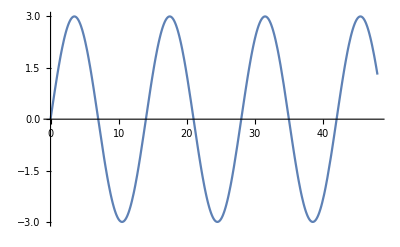

```mathematica
Plot[3Sin[(π x)/7],{x,0,48}]
```

```mathematica
a:=Sin[(π #)/7]&
FindRoot[NIntegrate[√(1+(a'[x])^2),{x,0,i}]==50,{i,45}]
```

NIntegrate::nlim: x = i is not a valid limit of integration.

{i→47.7289}

```mathematica
NIntegrate[√(1+(a'[x])^2),{x,0,47.729}]
```

50.0001

```mathematica
Integrate[(6x-3)*(8 x^2+4),{x,0,2}]
```

152

```mathematica
Integrate[q^3*Log[q],q]
```

-q^4/16+1/4 q^4 Log[q]

```mathematica
Integrate[10/((x-1)(x^2+9)),x]
```

10 (-1/30 ArcTan[x/3]-1/20 Log[10+2 (-1+x)+(-1+x)^2]+1/10 Log[-1+x])

```mathematica
Integrate[x^3/(√(x^2+49)),x]
```

1/3 (-98+x^2) √(49+x^2)

```mathematica
Table[x^2-4,{x,-4,4}]
```

{12,5,0,-3,-4,-3,0,5,12}

```mathematica
Manipulate[ParametricPlot[{Log[t],√t},{t,0,a}],{a,1,16}]
```